Construction of the Steiner system S(2,4,28) based on from Theorem 2.3 of:
Reid C., Rosa A., “Steiner systems S(2, 4, v) — a survey,” Electronic Journal of Combinatorics (2010)
The system S(2,4,28) consists of a set V of 28 elements, and a set B of length-4 subsets of V such that that every length-2 subset of V appears in exactly one element of B.  In other words, V is a list of players, B is a list of four-player matches, and every player plays every other player at exactly once.

```mathematica
Needs["FiniteFields`"]
```

### Generate matches

```mathematica
t=2;
v=12t+4;
pn=4t+1;
ℱ=GF[pn];
X=Table[ReduceElement[FromElementCode[ℱ,i]],{i,0,pn-1}];
Do[
If[Sort[Table[ReduceElement[a^n],{n,pn-1}]]==Sort[Rest[X]],
α=a;Break[]],
{a,X}];
c=1;
B=Flatten[Table[{
{{α^(2i)+j,1},{α^(2t+2i)+j,1},{α^(2i+c)+j,2},{α^(2t+2i+c)+j,2}},
{{α^(2i)+j,2},{α^(2t+2i)+j,2},{α^(2i+c)+j,3},{α^(2t+2i+c)+j,3}},
{{α^(2i)+j,3},{α^(2t+2i)+j,3},{α^(2i+c)+j,1},{α^(2t+2i+c)+j,1}},
{{∞},{j,1},{j,2},{j,3}}
},{i,0,t-1},{j,X}],2];
B=B/.{e:(_GF[___]):>ToElementCode[e]};
V=Union[Flatten[B,1]];
B=B/.Thread[V->Range[v]];
V=Range[v];
B=Union[Sort/@B]
```

{{1,2,3,4},{1,5,6,7},{1,8,9,10},{1,11,12,13},{1,14,15,16},{1,17,18,19},{1,20,21,22},{1,23,24,25},{1,26,27,28},{2,5,18,27},{2,6,21,23},{2,7,13,14},{2,8,15,24},{2,9,12,17},{2,10,22,26},{2,11,25,28},{2,16,19,20},{3,5,11,15},{3,6,19,28},{3,7,22,24},{3,8,20,27},{3,9,16,25},{3,10,13,18},{3,12,23,26},{3,14,17,21},{4,5,20,25},{4,6,12,16},{4,7,17,26},{4,8,11,19},{4,9,21,28},{4,10,14,23},{4,13,24,27},{4,15,18,22},{5,8,12,21},{5,9,24,26},{5,10,16,17},{5,13,19,23},{5,14,22,28},{6,8,14,18},{6,9,13,22},{6,10,25,27},{6,11,17,24},{6,15,20,26},{7,8,23,28},{7,9,15,19},{7,10,11,20},{7,12,18,25},{7,16,21,27},{8,13,16,26},{8,17,22,25},{9,11,14,27},{9,18,20,23},{10,12,15,28},{10,19,21,24},{11,16,22,23},{11,18,21,26},{12,14,20,24},{12,19,22,27},{13,15,21,25},{13,17,20,28},{14,19,25,26},{15,17,23,27},{16,18,24,28}}

### Split matches into rounds

```mathematica
f[list_,remaining_]:=If[
remaining=={},
list,
Block[{return=None,next=First[remaining],rest=Rest[remaining]},
Do[
If[Intersection[Flatten[list[[i]]],next]=={},
return=f[MapAt[Append[#,next]&,list,i],rest];
If[return===None,
,
Break[];
]
],
{i,Length[list]}];
return]
]
sets=f[ConstantArray[{},9],B]
```

{{{1,2,3,4},{5,8,12,21},{6,9,13,22},{7,10,11,20},{14,19,25,26},{15,17,23,27},{16,18,24,28}},{{1,5,6,7},{2,8,15,24},{3,9,16,25},{4,10,14,23},{11,18,21,26},{12,19,22,27},{13,17,20,28}},{{1,8,9,10},{2,5,18,27},{3,6,19,28},{4,7,17,26},{11,16,22,23},{12,14,20,24},{13,15,21,25}},{{1,11,12,13},{2,16,19,20},{3,14,17,21},{4,15,18,22},{5,9,24,26},{6,10,25,27},{7,8,23,28}},{{1,14,15,16},{2,10,22,26},{3,8,20,27},{4,9,21,28},{5,13,19,23},{6,11,17,24},{7,12,18,25}},{{1,17,18,19},{2,6,21,23},{3,7,22,24},{4,5,20,25},{8,13,16,26},{9,11,14,27},{10,12,15,28}},{{1,20,21,22},{2,11,25,28},{3,12,23,26},{4,13,24,27},{5,10,16,17},{6,8,14,18},{7,9,15,19}},{{1,23,24,25},{2,9,12,17},{3,10,13,18},{4,8,11,19},{5,14,22,28},{6,15,20,26},{7,16,21,27}},{{1,26,27,28},{2,7,13,14},{3,5,11,15},{4,6,12,16},{8,17,22,25},{9,18,20,23},{10,19,21,24}}}

### Order matches/rounds

```mathematica
g[list_,remaining_,n_]:=If[
remaining=={},
list,
Block[{return=None},
Do[
If[Intersection[Flatten[list[[-n;;]]],choice]=={},
return=g[Append[list,choice],If[Length[First[remaining]]==1,Rest[remaining],Prepend[Rest[remaining],DeleteCases[First[remaining],choice]]],n];
If[return===None,
,
Break[];
]
],
{choice,First[remaining]}];
return]
]
best={{},0};
Dynamic[best]
n=0;
Do[While[True,current=g[First[s],Rest[s],n];If[current===None,Break[],best={current,n}];n++],{s,Permutations[sets]}];
ordering=First[best];
```

### Visualization

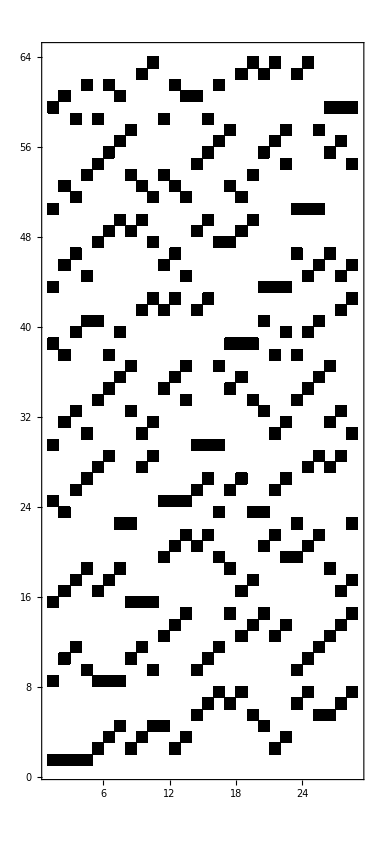

```mathematica
positions=(Flatten/@Flatten[MapIndexed[List,ordering,{2}],1])[[;;,;;2]];
Graphics[Rectangle/@positions,GridLines->{Range,Range},PlotRange->{{0,28}+1,{0,63}+1},Frame->True,Ticks->{Range,Range}]
```